InterpolatingFunction::dmval: Input value {2.20146×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

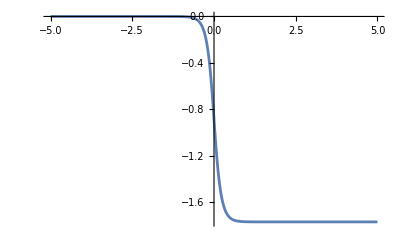

```mathematica
(*Import Steady-State soliton for g/\kappa=0.2*)
κ=7.5;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k7p5"];
Phi7p5=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss7p5[x_]:=Phi7p5[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])]; (*Coordinate transform from imported asymptotic coordinates*)
Plot[ϕss7p5[x],{x,-5,5}]
```

InterpolatingFunction::dmval: Input value {3.82358×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

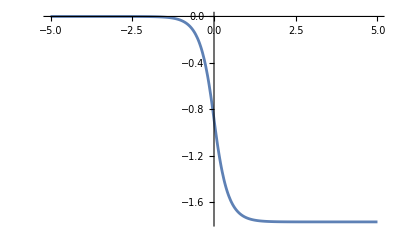

```mathematica
(*Import Steady-State soliton for g/\kappa=1*)
κ=1.5;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k1p5"];
Phi1p5=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss1p5[x_]:=Phi1p5[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
Plot[ϕss1p5[x],{x,-5,5}]
```

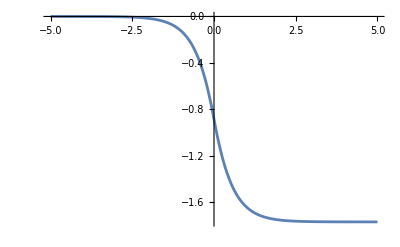

```mathematica
(*Import Steady-State soliton for g/\kappa=5*)
κ=0.3;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k0p3"];
Phi0p3=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss0p3[x_]:=Phi0p3[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
Plot[ϕss0p3[x],{x,-5,5}]
```

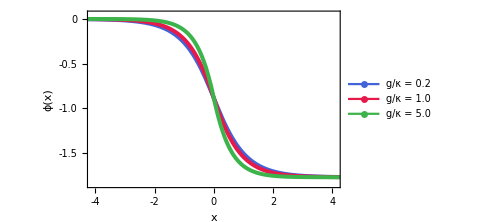

```mathematica
(*Making the pretty figure of ϕ*)
col3=RGBColor[.235,.706,.294];
col2=RGBColor[.902,.097,.294];
col1=RGBColor[.263,.388,.847];

phiplot=Plot[{ϕss7p5[x],ϕss1p5[x],ϕss0p3[x]},{x,-5,5},PlotStyle->{{col1,Thickness[0.008]},{col2,Thickness[0.008]},{col3,Thickness[0.008]}},PlotRange->{{-4.1,4.1},{-1.85,0.05}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{{{0,"0"},{-0.5,"-0.5"},{-1.0,"-1.0"},{-1.5,"-1.5"}},None },{{{-4,"-4"},{-2,"-2"},{0,"0"},{2,"2"},{4,"4"}},None }},FrameTicksStyle->Directive[Black,12],FrameLabel->{Style["x",Italic,14],Style["ϕ(x)",14]},PlotLegends->Placed[LineLegend[{col1,col2,col3},{Style["g/κ = 0.2",12],Style["g/κ = 1.0",12],Style["g/κ = 5.0",12]},LegendMarkers->{{Graphics[{col1,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}},{Graphics[{col2,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}},{Graphics[{col3,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}}},LegendLayout->"Column"],{0.21,0.30} ],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},ImageSize->5*72,ImagePadding->{{55,15},{40,15}},Background->White]
```

```mathematica
(*Undo comment here if you want to export figure*)
(*Export["/Users/zoe/Documents/AtomPaperFigures/fig1phi_original.pdf",phiplot,ImageResolution->600]*)
```

```mathematica
(*Derivatives of ϕ, proportional to charge density*)
ρ7p5[x_]:=D[ϕss7p5[X],X]/. X->x;
ρ1p5[x_]:=D[ϕss1p5[X],X]/. X->x;
ρ0p3[x_]:=D[ϕss0p3[X],X]/. X->x;
```

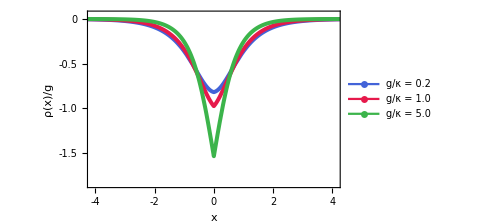

```mathematica
(*Pretty figure of ρ/g*)
rhoplot=Plot[{ρ7p5[x],ρ1p5[x],ρ0p3[x]},{x,-5,5},PlotStyle->{{col1,Thickness[0.008]},{col2,Thickness[0.008]},{col3,Thickness[0.008]}},PlotRange->{{-4.1,4.1},{-1.85,0.05}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{{{0,"0"},{-0.5,"-0.5"},{-1.0,"-1.0"},{-1.5,"-1.5"}},None },{{{-4,"-4"},{-2,"-2"},{0,"0"},{2,"2"},{4,"4"}},None}},FrameTicksStyle->Directive[Black,12],FrameLabel->{Style["x",Italic,14],Style["ρ(x)/g",14]},PlotLegends->Placed[LineLegend[{col1,col2,col3},{Style["g/κ = 0.2",12],Style["g/κ = 1.0",12],Style["g/κ = 5.0",12]},LegendMarkers->{{Graphics[{col1,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}},{Graphics[{col2,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}},{Graphics[{col3,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}}},LegendLayout->"Column"],{0.21,0.30}],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},ImageSize->5*72,ImagePadding->{{55,15},{40,15}},Background->White]
```

```mathematica
(*Export["/Users/zoe/Documents/AtomPaperFigures/fig1rho_original.pdf",rhoplot,ImageResolution->600]*)
```

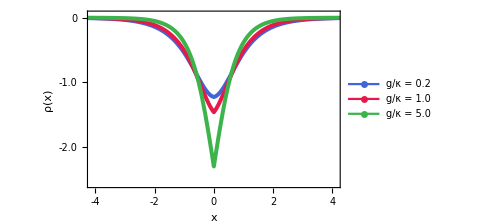

```mathematica
(*Pretty figure of charge density*)
rhoplotscaled=Plot[{g*ρ7p5[x],g*ρ1p5[x],g*ρ0p3[x]},{x,-5,5},PlotStyle->{{col1,Thickness[0.008]},{col2,Thickness[0.008]},{col3,Thickness[0.008]}},PlotRange->{{-4.1,4.1},{-2.58,0.05}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{{{0,"0"},{-0.5,"-0.5"},{-1.0,"-1.0"},{-1.5,"-1.5"},{-2.0,"-2.0"},{-2.5,"-2.5"}},None },{{{-4,"-4"},{-2,"-2"},{0,"0"},{2,"2"},{4,"4"}},None}},FrameTicksStyle->Directive[Black,12],FrameLabel->{Style["x",Italic,14],Style["ρ(x)",14]},PlotLegends->Placed[LineLegend[{col1,col2,col3},{Style["g/κ = 0.2",12],Style["g/κ = 1.0",12],Style["g/κ = 5.0",12]},LegendMarkers->{{Graphics[{col1,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}},{Graphics[{col2,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}},{Graphics[{col3,Thickness[0.1],Line[{{0,0},{1,0}}]}],{30,10}}},LegendLayout->"Column"],{0.21,0.30}],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},ImageSize->5*72,ImagePadding->{{55,15},{40,15}},Background->White]
```

```mathematica
(*Export["/Users/zoe/Documents/AtomPaperFigures/fig1rhoscaled_original.pdf",rhoplotscaled,ImageResolution->600]*)
```